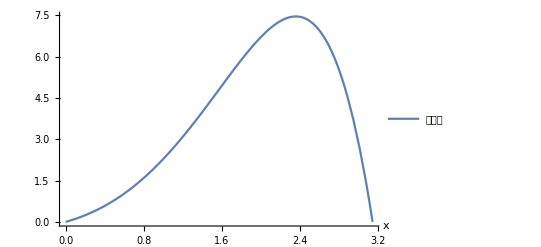

20

{{0.,1.21649×10^-13},{0.15708,0.180712},{0.314159,0.418397},{0.471239,0.720222},{0.628319,1.09231},{0.785398,1.539},{0.942478,2.06193},{1.09956,2.65895},{1.25664,3.32283},{1.41372,4.03983},{1.5708,4.78805},{1.72788,5.53572},{1.88496,6.23935},{2.04204,6.84195},{2.19911,7.2713},{2.35619,7.43852},{2.51327,7.23704},{2.67035,6.54221},{2.82743,5.21186},{2.98451,3.08797},{3.14159,0.}}

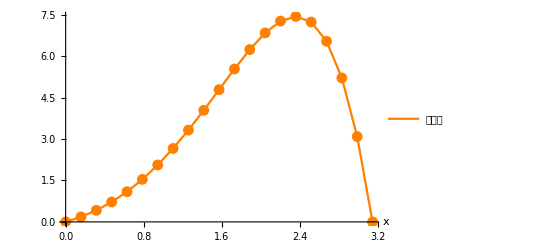

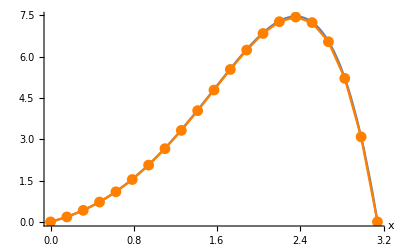

```mathematica
Clear[u,b,NN,v,f,A];
f[x_]=E^x*(Sin[x]-2*Cos[x]);
v[x_]=E^x*Sin[x];
p1=Plot[v[x],{x,0,Pi},PlotRange->All,AxesLabel->Automatic,PlotLegends->Placed[{"精确解"},{Scaled[{0.1,1}],{0,1}}]]
l=Pi;h=0.05*Pi;NN=IntegerPart[l/h]
u=Array[U,NN+1];
b=Array[B,NN+1];
b[[1]]=0;b[[NN+1]]=0;
u[[1]]=0;u[[NN+1]]=0;
A=SparseArray[{{i_,i_}->1+2/h^2,{i_,j_}/;Abs[i-j]==1->-1/h^2},{NN+1,NN+1}];
A[[1,1]]=1;A[[NN+1,NN+1]]=1;A[[1,2]]=0;A[[NN+1,NN]]=0;
For[j=2,j≤NN,j++,
b[[j]]=f[(j-1)*h];
]
u[[;;]]=LinearSolve[A,b];
data=Table[{(j-1)*h,u[[j]]},{j,1,NN+1}]
p2=ListLinePlot[data,AxesLabel->{x},PlotRange->All,Mesh->All,PlotStyle->Orange,PlotLegends->Placed[{"数值解"},{Scaled[{0.1,1}],{0,1}}]]
Show[p1,p2,PlotRange->All]
```